```mathematica
SetDirectory[NotebookDirectory[]];
ips=SequenceSplit[Import["pressure.ssv","Table"],{{}}];
ids=SequenceSplit[Import["density.ssv","Table"],{{}}];
iks=SequenceSplit[Import["hc-ratio.ssv","Table"],{{}}];
ivs=SequenceSplit[Import["velocity.ssv","Table"],{{}}];
its=SequenceSplit[Import["temperature.ssv","Table"],{{}}];
```

```mathematica
ps=Map[Flatten[Table[{j-1,i-1,#⟦i⟧⟦j⟧},{i,1,Length@#},{j,1,Length@First@#}], 1]&,ips];
pminmax=MinMax@Map[#⟦3⟧&,Flatten[ps,1]];
pcolorfn=ColorData["M10DefaultDensityGradient"];
psPlots=Table[ListDensityPlot[ps⟦i⟧,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,
ColorFunctionScaling->False,ColorFunction->(pcolorfn[(#-pminmax⟦1⟧)/(pminmax⟦2⟧-pminmax⟦1⟧)]&)],
{i,1,Length@ps}];
```

```mathematica
Export["pressure.avi",psPlots];
```

```mathematica
Manipulate[psPlots⟦i⟧,{i,1,Length@ps,1}]
```

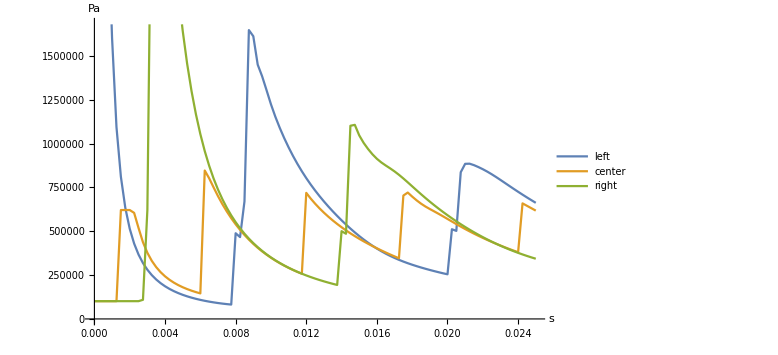

```mathematica
rpsCurves=Table[ips⟦t⟧⟦1⟧⟦z⟧,{z,Dimensions[ips]⟦3⟧},{t,Length@ips}];
ListLinePlot[Map[Table[{(i-1)250 10^-6,rpsCurves⟦#⟧⟦i⟧},{i,Length@rpsCurves⟦#⟧}]&,{20,250,480}],PlotLegends->{"left","center","right"},TargetUnits->{"Seconds","Pascals"},AxesLabel->Automatic,ImageSize->Large]
Export["pressure.png",%];
```

```mathematica
ds=Map[Flatten[Table[{j-1,i-1,#⟦i⟧⟦j⟧},{i,1,Length@#},{j,1,Length@First@#}], 1]&,ids];
dminmax=MinMax@Map[#⟦3⟧&,Flatten[ds,1]];
dcolorfn=ColorData["M10DefaultDensityGradient"];
dsPlots=Table[ListDensityPlot[ds⟦i⟧,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,
ColorFunctionScaling->False,ColorFunction->(dcolorfn[(#-dminmax⟦1⟧)/(dminmax⟦2⟧-dminmax⟦1⟧)]&)],
{i,1,Length@ds}];
```

```mathematica
Export["density.avi",dsPlots];
```

```mathematica
Manipulate[dsPlots⟦i⟧,{i,1,Length@ds,1}]
```

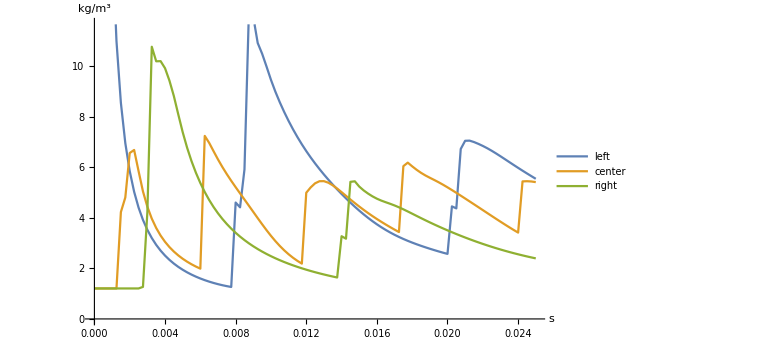

```mathematica
rdsCurves=Table[ids⟦t⟧⟦1⟧⟦z⟧,{z,Dimensions[ids]⟦3⟧},{t,Length@ids}];
ListLinePlot[Map[Table[{(i-1)250 10^-6,rdsCurves⟦#⟧⟦i⟧},{i,Length@rdsCurves⟦#⟧}]&,{20,250,480}],PlotLegends->{"left","center","right"},TargetUnits->{"Seconds","Kilograms"/("Meters")^3},AxesLabel->Automatic,ImageSize->Large]
Export["density.png",%];
```

```mathematica
ks=Map[Flatten[Table[{j-1,i-1,#⟦i⟧⟦j⟧},{i,1,Length@#},{j,1,Length@First@#}], 1]&,iks];
kminmax=MinMax@Map[#⟦3⟧&,Flatten[ks,1]];
kcolorfn=ColorData["M10DefaultDensityGradient"];
ksPlots=Table[ListDensityPlot[ks⟦i⟧,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,
ColorFunctionScaling->False,ColorFunction->(kcolorfn[(#-kminmax⟦1⟧)/(kminmax⟦2⟧-kminmax⟦1⟧)]&)],
{i,1,Length@ks}];
```

```mathematica
Export["hc-ratio.avi",ksPlots];
```

```mathematica
Manipulate[ksPlots⟦i⟧,{i,1,Length@ks,1}]
```

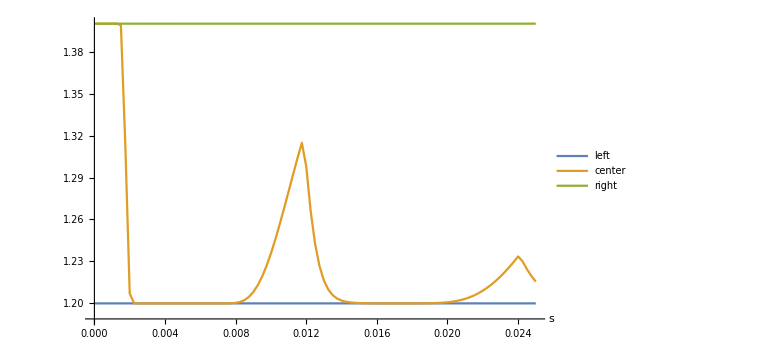

```mathematica
rksCurves=Table[iks⟦t⟧⟦1⟧⟦z⟧,{z,Dimensions[iks]⟦3⟧},{t,Length@iks}];
ListLinePlot[Map[Table[{(i-1)250 10^-6,rksCurves⟦#⟧⟦i⟧},{i,Length@rksCurves⟦#⟧}]&,{20,250,480}],PlotLegends->{"left","center","right"},TargetUnits->{"Seconds",""},AxesLabel->Automatic,ImageSize->Large]
Export["hc-ratio.png",%];
```

```mathematica
ts=Map[Flatten[Table[{j-1,i-1,#⟦i⟧⟦j⟧},{i,1,Length@#},{j,1,Length@First@#}], 1]&,its];
tminmax=MinMax@Map[#⟦3⟧&,Flatten[ts,1]];
tcolorfn=ColorData["TemperatureMap"];
tsPlots=Table[ListDensityPlot[ts⟦i⟧,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,
ColorFunctionScaling->False,ColorFunction->(tcolorfn[(#-tminmax⟦1⟧)/(tminmax⟦2⟧-tminmax⟦1⟧)]&)],
{i,1,Length@ts}];
```

```mathematica
Export["temperature.avi",tsPlots];
```

```mathematica
Manipulate[tsPlots⟦IntegerPart[i]⟧,{i,1,Length@ts,1}]
```

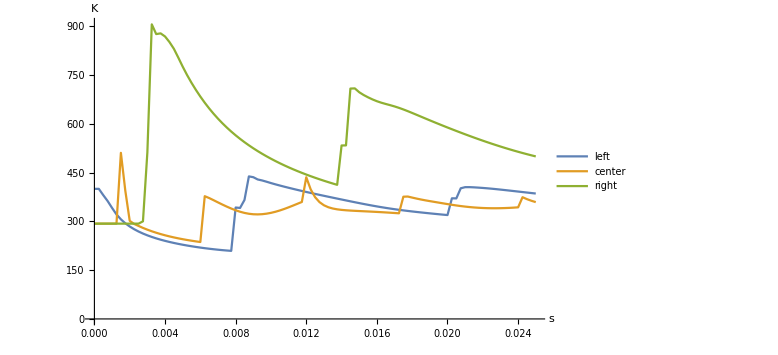

```mathematica
rtsCurves=Table[its⟦t⟧⟦1⟧⟦z⟧,{z,Dimensions[its]⟦3⟧},{t,Length@its}];
ListLinePlot[Map[Table[{(i-1)250 10^-6,rtsCurves⟦#⟧⟦i⟧},{i,Length@rtsCurves⟦#⟧}]&,{20,250,480}],PlotLegends->{"left","center","right"},TargetUnits->{"Seconds","Kelvins"},AxesLabel->Automatic,ImageSize->Large]
Export["temperature.png",%];
```

```mathematica
vs=Map[Table[{{(j-1)/2,i-1},{#⟦i⟧⟦j⟧,#⟦i⟧⟦j+1⟧}},{i,1,Length@#},{j,1,Length@First@#,2}]&,ivs];
vsPlots=Table[ListVectorPlot[vs⟦i⟧,PlotRange->{{0,499},{0,9}},ImageSize->Large],{i,1,Length@vs}];
```

```mathematica
Export["velocity.avi",vsPlots];
```

```mathematica
Manipulate[vsPlots⟦IntegerPart[i]⟧,{i,1,Length@vs,1}]
```

```mathematica
toVm={#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧,Sqrt[(#⟦2⟧⟦1⟧)^2+(#⟦2⟧⟦2⟧)^2]}&;
Off[General::munfl]
vms=Map[With[{els=Flatten[#,1]},Map[toVm,els]]&,vs];
```

```mathematica
vmminmax=MinMax@Map[#⟦3⟧&,Flatten[vms,1]];
vmcolorfn=ColorData["M10DefaultDensityGradient"];
vmsPlots=Table[ListDensityPlot[vms⟦i⟧,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,
ColorFunctionScaling->False,ColorFunction->(vmcolorfn[(#-vmminmax⟦1⟧)/(vmminmax⟦2⟧-vmminmax⟦1⟧)]&)],
{i,1,Length@vms}];
```

```mathematica
Export["velmagn.avi",kinsPlots];
```

```mathematica
Manipulate[vmsPlots⟦IntegerPart[i]⟧,
{i,1,Length@vms,1}]
```

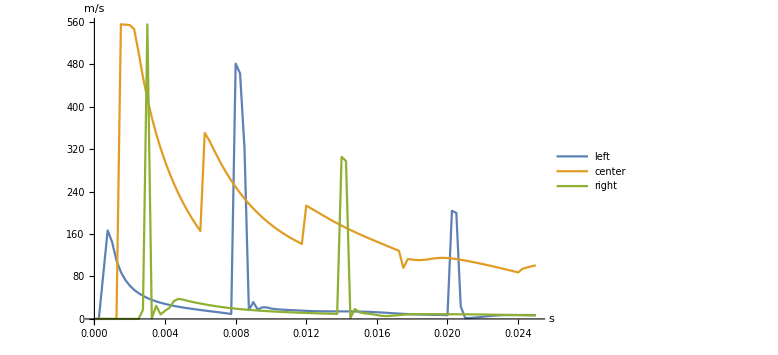

```mathematica
rvmsCurves=Table[vms⟦t⟧⟦z⟧⟦3⟧,{z,Dimensions[ips]⟦3⟧},{t,Length@ips}];
ListLinePlot[Map[Table[{(i-1)250 10^-6,rvmsCurves⟦#⟧⟦i⟧},{i,Length@rvmsCurves⟦#⟧}]&,{20,250,480}],PlotLegends->{"left","center","right"},TargetUnits->{"Seconds","Meters"/"Seconds"},AxesLabel->Automatic,ImageSize->Large]
Export["velmagn.png",%];
```